```mathematica
path = "/home/michal4/Documents/studia/uj-spe/lab02/docs/plots/";
rawData = Import[path<>"results-rlc-4-filtered.csv","CSV"];
rawData = Drop[rawData,1];
```

```mathematica
fitData = {#2,#4/#3}&@@@rawData;
R=1776;
model = NonlinearModelFit[
fitData,
{R/(R+Abs[1/(1/(x 2 Pi L)-x 2 Pi c)]),L>0,L<10^-2,c>0,c<10^-8},{L,c}, x,Method->"NMinimize"];
bestFit = model["BestFitParameters"]
valL = bestFit[[1]][[2]];
valC = bestFit[[2]][[2]];
1/(2 Pi Sqrt[valL valC])
```

{L→0.00826593,c→4.43375×10^-9}

26289.9

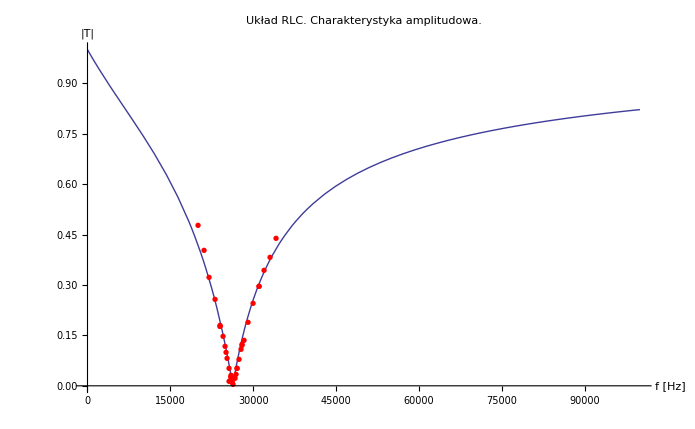

```mathematica
Show[
Plot[model[x],{x,0,100000},
PlotRange->{Automatic,{0,1}},
BaseStyle->{FontSize->16},
PlotLabel-> "Układ RLC. Charakterystyka amplitudowa.",
AxesLabel->{"f [Hz]","|T|"}],
ListPlot[fitData,PlotMarkers->{Automatic,7},PlotStyle->Red]
]
```

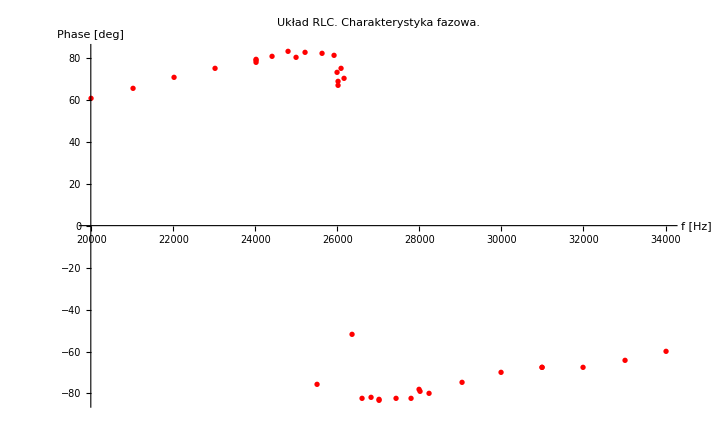

```mathematica
Show[
ListPlot[ {#2,#5}&@@@rawData,
PlotMarkers->{Automatic,7},
PlotStyle->Red,
BaseStyle->{FontSize->16},
PlotLabel-> "Układ RLC. Charakterystyka fazowa.",
AxesLabel->{"f [Hz]","Phase [deg]"}]
]
```